```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Problem 3*)
T=(1/2) m (y1t^2+z1t^2 + y2t^2+z2t^2)
V=m g (z1 + z2);
y1=l1 Sin[θ1];     
y2=l1 Sin[θ1]+l2 Sin[θ2]; 
z1 = -l1 Cos[θ1]; 
z2= -l1 Cos[θ1] - l2 Cos[θ2]; 
y1t=D[y1,θ1] θ1t;
y2t=D[y2,θ1] θ1t+D[y2,θ2] θ2t;
z1t=D[z1,θ1] θ1t;
z2t=D[z2,θ1] θ1t+D[z2,θ2] θ2t;
τ = c θ1t;
```

1/2 m (y1t^2+y2t^2+z1t^2+z2t^2)

```mathematica
T=Collect[T,{θ1t,θ2t},Simplify]
V=Simplify[V]
```

θ1t^2 l1^2 m+θ1t θ2t l1 l2 m cos(θ1-θ2)+1/2 θ2t^2 l2^2 m

-g m (2 l1 cos(θ1)+l2 cos(θ2))

```mathematica
(*First E-L equation*)
L=T-V;
D[L,θ1t];
D[%,θ1] θ1t+D[%,θ2] θ2t+D[%,θ1t]θ1tt+D[%,θ2t] θ2tt ;
D[L,θ1];
eqn1=Simplify[%%-%]
```

l1 m (2 g sin(θ1)+2 θ1tt l1+θ2t^2 l2 sin(θ1-θ2)+θ2tt l2 cos(θ1-θ2))

```mathematica
(*Second E-L equation*)
D[L,θ2t];
D[%,θ1] θ1t+D[%,θ2] θ2t +D[%,θ1t]θ1tt+D[%,θ2t] θ2tt;
D[L,θ2];
eqn2=Simplify[%%-%]
```

l2 m (g sin(θ2)+θ1t^2 (-l1) sin(θ1-θ2)+θ1tt l1 cos(θ1-θ2)+θ2tt l2)

```mathematica
(*Linearize first E-L equation. Trigonometric simplifications*)
leqn1=(eqn1 + τ)/.{Sin[θ1]->θ1,Cos[θ1-θ2]->1,Sin[θ1-θ2]->θ1-θ2,Cos[θ2]->1};
Expand[%];
%/.{θ2t^2->0};
leqn1=Simplify[%]
```

c θ1t+2 g θ1 l1 m+l1 m (2 θ1tt l1+θ2tt l2)

```mathematica
(*Linearize second E-L equation. Trigonometric simplifications*)
leqn2=eqn2/.{Sin[θ1]->θ1,Cos[θ1-θ2]->1,Sin[θ1-θ2]->θ1-θ2,Cos[θ2]->1, Sin[θ2]->θ2};
Expand[%];
%/.{θ1t^2->0};
leqn2=Simplify[%]
```

l2 m (g θ2+θ1tt l1+θ2tt l2)

```mathematica
nleqn1=Collect[leqn1 +τ/. {θ1tt->s^2 θ1, θ2tt->s^2 θ2, θ1t-> s θ1},{θ1,θ2, θ3},Simplify]
nleqn2=Collect[leqn2 /. {θ1tt->s^2 θ1, θ2tt->s^2 θ2},{θ1,θ2,θ3},Simplify]
```

2 θ1 (s (c+l1^2 m s)+g l1 m)+θ2 l1 l2 m s^2

θ2 l2 m (g+l2 s^2)+θ1 l1 l2 m s^2

```mathematica
(*CoefficientArrays[{nleqn1, nleqn2, nleqn3}, {θ1, θ2, θ3}];*)
A = {{nleqn1[[1]]/.{θ1->1}, nleqn1[[2]]/.{θ2->1}},
{nleqn2[[1]]/.{θ1->1}, nleqn2[[2]]/.{θ2->1}}}
```

(2 (g l1 m+s (m s l1^2+c)) | l1 l2 m s^2
l1 l2 m s^2 | l2 m (l2 s^2+g))

```mathematica
(* Characteristic Polynomial *)
cp=Collect[Det[A],s,Simplify]
```

2 c g l2 m s+2 c l2^2 m s^3+2 g^2 l1 l2 m^2+2 g l1 l2 m^2 s^2 (l1+l2)+l1^2 l2^2 m^2 s^4

```mathematica
soln=Solve[cp==0,s];
```

```mathematica
s1=s/.soln⟦2⟧;
s2=s/.soln⟦4⟧;
```

-5-1/2 √(1846/25+1/3 (1/2 (20457870138/15625+(8829 √(23197675970643/2))/15625))^(1/3)-660213/(125 2^(2/3) (20457870138/15625+(8829 √(23197675970643/2))/15625)^(1/3)))+1/2 √(3692/25-1/3 (1/2 (20457870138/15625+(8829 √(23197675970643/2))/15625))^(1/3)+660213/(125 2^(2/3) (20457870138/15625+(8829 √(23197675970643/2))/15625)^(1/3))+8038/(5 √(1846/25+1/3 (1/2 (20457870138/15625+(8829 √(23197675970643/2))/15625))^(1/3)-660213/(125 2^(2/3) (20457870138/15625+(8829 √(23197675970643/2))/15625)^(1/3)))))

```mathematica
(*nwsq1=s1/.parameters;
nwsq2=s2/.parameters;
N[nwsq1]
N[nwsq2]
*)
```

-0.5 √(0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)+(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))+c^2-26.16)+0.5 √(-0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)-(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))-(0.25 (156.96 c-8. c^3))/(√(0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)+(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))+c^2-26.16))+2. c^2-52.32)-0.5 c

0.5 √(0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)+(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))+c^2-26.16)+0.5 √(-0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)-(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))+(0.25 (156.96 c-8. c^3))/(√(0.264567 (√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3)+(0.419974 (3849.44-117.72 c^2))/((√((17322.5 c^2-422946.)^2-4. (3849.44-117.72 c^2)^3)+17322.5 c^2-422946.)^(1/3))+c^2-26.16))+2. c^2-52.32)-0.5 c

```mathematica
f = {{-Τ0},{Τ0}}
```

(-Τ0
Τ0)

```mathematica
θ1func = Simplify[(((Inverse[A].f ) Exp[s t] /. {s-> I wf}))[[1,1]]]
θ2func = Simplify[(((Inverse[A].f)Exp[s t]/. {s-> I wf}))[[2,1]]]
```

-(Τ0 ⅇ^(ⅈ t wf) (g-wf^2 (l1+l2)))/(-2 g wf (l1 m wf (l1+l2)-ⅈ c)+l2 wf^3 (l1^2 m wf-2 ⅈ c)+2 g^2 l1 m)

(Τ0 ⅇ^(ⅈ t wf) (2 g l1 m-wf (l1 m wf (2 l1+l2)-2 ⅈ c)))/(l2 m (-2 g wf (l1 m wf (l1+l2)-ⅈ c)+l2 wf^3 (l1^2 m wf-2 ⅈ c)+2 g^2 l1 m))

```mathematica
ComplexExpand[θ1func]
```

(l1^2 l2^2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(l1^3 l2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l2^2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1 l2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1^3 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1 l2^2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(5 g l1^2 l2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c g l1 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 c g l2 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1^2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1 l2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c g^2 Τ0 sin(t wf) wf)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g^3 l1 m Τ0 cos(t wf))/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+ⅈ ((l1^2 l2^2 m Τ0 sin(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(l1^3 l2 m Τ0 sin(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l2^2 Τ0 cos(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1 l2 Τ0 cos(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1^3 m Τ0 sin(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1 l2^2 m Τ0 sin(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(5 g l1^2 l2 m Τ0 sin(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c g l1 Τ0 cos(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(4 c g l2 Τ0 cos(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1^2 m Τ0 sin(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1 l2 m Τ0 sin(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c g^2 Τ0 cos(t wf) wf)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g^3 l1 m Τ0 sin(t wf))/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))

```mathematica
ComplexExpand[θ2func]
```

-(2 l1^4 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(l1^3 l2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1^2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1 l2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(8 g l1^3 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 g l1^2 l2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g l1^4 m Τ0 cos(t wf) wf^4)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(4 c^2 Τ0 cos(t wf) wf^4)/(m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(2 c g l1 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(6 g^2 l1^2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(8 g^2 l1^3 m Τ0 cos(t wf) wf^2)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 c^2 g Τ0 cos(t wf) wf^2)/(l2 m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 g^3 l1^2 m Τ0 cos(t wf))/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+ⅈ (-(2 l1^4 m Τ0 sin(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(l1^3 l2 m Τ0 sin(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1^2 Τ0 cos(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1 l2 Τ0 cos(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(8 g l1^3 m Τ0 sin(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 g l1^2 l2 m Τ0 sin(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g l1^4 m Τ0 sin(t wf) wf^4)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(4 c^2 Τ0 sin(t wf) wf^4)/(m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(2 c g l1 Τ0 cos(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(6 g^2 l1^2 m Τ0 sin(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(8 g^2 l1^3 m Τ0 sin(t wf) wf^2)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 c^2 g Τ0 sin(t wf) wf^2)/(l2 m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 g^3 l1^2 m Τ0 sin(t wf))/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)))

```mathematica
yp = {(l1^2 l2^2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(l1^3 l2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l2^2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1 l2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1^3 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1 l2^2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(5 g l1^2 l2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c g l1 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 c g l2 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1^2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1 l2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c g^2 Τ0 Sin[t wf] wf)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g^3 l1 m Τ0 Cos[t wf])/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2),-(2 l1^4 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(l1^3 l2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1^2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1 l2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(8 g l1^3 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 g l1^2 l2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g l1^4 m Τ0 Cos[t wf] wf^4)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(4 c^2 Τ0 Cos[t wf] wf^4)/(m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(2 c g l1 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(6 g^2 l1^2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(8 g^2 l1^3 m Τ0 Cos[t wf] wf^2)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 c^2 g Τ0 Cos[t wf] wf^2)/(l2 m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 g^3 l1^2 m Τ0 Cos[t wf])/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))}
```

{(l1^2 l2^2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(l1^3 l2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l2^2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1 l2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1^3 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1 l2^2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(5 g l1^2 l2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c g l1 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 c g l2 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1^2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1 l2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c g^2 Τ0 sin(t wf) wf)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g^3 l1 m Τ0 cos(t wf))/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2),-(2 l1^4 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(l1^3 l2 m Τ0 cos(t wf) wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1^2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1 l2 Τ0 sin(t wf) wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(8 g l1^3 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 g l1^2 l2 m Τ0 cos(t wf) wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g l1^4 m Τ0 cos(t wf) wf^4)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(4 c^2 Τ0 cos(t wf) wf^4)/(m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(2 c g l1 Τ0 sin(t wf) wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(6 g^2 l1^2 m Τ0 cos(t wf) wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(8 g^2 l1^3 m Τ0 cos(t wf) wf^2)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 c^2 g Τ0 cos(t wf) wf^2)/(l2 m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 g^3 l1^2 m Τ0 cos(t wf))/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))}

```mathematica
Clear[Τ0,wf]
```

```mathematica
ypplot
```

{-(34403050000 sin(t))/602450897921-(301138370500 cos(t))/602450897921,(649644791000 cos(t))/602450897921-(3905000000 sin(t))/602450897921}

```mathematica
(* T0 = 1/15 at c=10,000. w = .855 rad/sec *)
```

{-(34403050000000 sin(t))/776161594689287921-(30113837050 cos(t))/776161594689287921,(88100064083479100 cos(t))/776161594689287921-(3905000000000 sin(t))/776161594689287921}

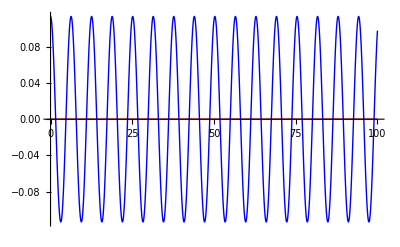

```mathematica
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->1, wf->1, c->10000};
ypplot = yp /.parameters
Plot[ypplot, {t,0,100}, PlotStyle->{Red, Blue}]
```

```mathematica
nA=A/.parameters;
nA//MatrixForm
```

(2 (s (s+1)+981/100) | s^2
s^2 | s^2+981/100)

```mathematica
(*(V1=Simplify[(genericV/.wsq->nwsq1)])//MatrixForm
(V2=Simplify[(genericV/.wsq->nwsq2)])//MatrixForm*)
```

```mathematica
(*N[%%%]
N[%%%]*)
```

```mathematica
(*Simplify[(nA/.wsq->nwsq1).V1]
Simplify[(nA/.wsq->nwsq2).V2]*)
```

```mathematica
(*ω1 = Sqrt[nwsq1]
ω2=Sqrt[nwsq2]*)
```

```mathematica
(*nA/.wsq->nwsq1 *)
```

```mathematica
(*(nA/.wsq->nwsq1).V1*)
```